```mathematica
(* Compute the list of all possible Events where i is number rentals and j is number of returns*)
events = Table[{i,j},{i,0,20},{j,0,20}];

(* Compute the list of all possible Events where i is number cars at lot1 and j is number of cars at lot2 *)
states = Table[{i,j},{i,0,20},{j,0,20}];

(* initialize all actions, π(s) to 0 *)
Table[pi[{i,j}] = 0,{i,0,20},{j,0,20}];

(* initialize state values, V, to 0 *)
Table[V[{i,j}]=0,{i,0,20},{j,0,20}];
```

```mathematica
(*compute the event probability of N rentals and M returns given Subscript[λ, rental] and Subscript[λ, return] *)
P[λ_List,n_List]:=Times@@MapThread[N[PDF[PoissonDistribution[#1],#2]]&,{λ,n}]
```

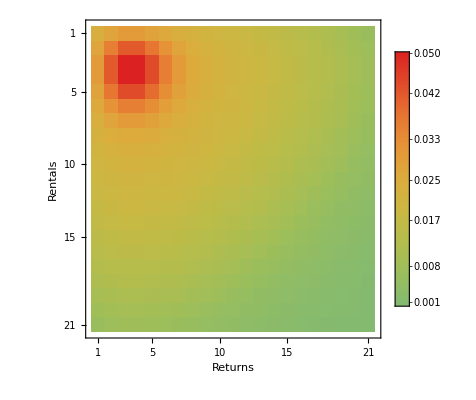

```mathematica
(* visualize event likelihoods with Subscript[λ, rental] = 3 and Subscript[λ, return] = 4*)
MatrixPlot[Map[P[{3,3},#]&,events,{2}],PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"Rentals","Returns"}]
```

```mathematica
(* Compute possible events to get from N resouces at time t to M resources at t+1 *)
Events[nstart_,nstop_]:= Module[
{dN,minRentals,maxRentals},
dN = nstop - nstart; minRentals = Abs[Min[0,dN]];  maxRentals = nstart;
Table[{nrent,dN+nrent},{nrent,minRentals,maxRentals}]
];
```

```mathematica
(* compute the transition probability from state with N cars to state with M cars *)
T[nstart_,nstop_,λ_List] :=Total[Map[P[λ,#]&,Events[nstart,nstop]]];
```

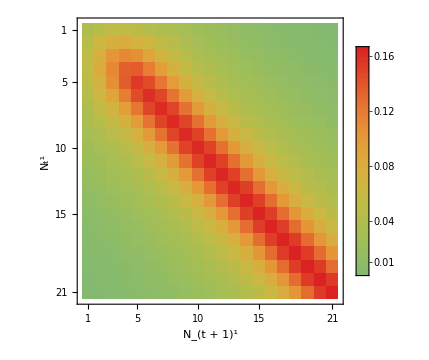
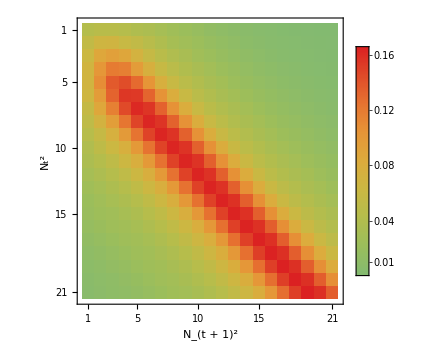
-Graphics- | -Graphics-

```mathematica
(* show all transition probabilities for both car lots *)
Grid[{{
MatrixPlot[
Table[T[i,j,{3,3}],{i,0,20},{j,0,20}],
ImageSize->Medium, PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"N_t^1","N_(t + 1)^1"}],
MatrixPlot[
Table[T[i,j,{4,2}],{i,0,20},{j,0,20}],
ImageSize->Medium,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"N_t^2","N_(t + 1)^2"}]
}}]
```

```mathematica
(* helper function to compute joint transition probability for both car lots (resource pools)*)
TT[nstart_List,nstop_List,Λ_List]:=Times@@MapThread[T,{nstart,nstop,Λ}]
```

```mathematica
(* compute transition probability from s = {4,4} to state s'={6,9} given event likelihood parameters Λ = {λ1,λ2}*)
TT[{5,7},{6,9},{{3,3},{4,2}}]
```

0.0062471

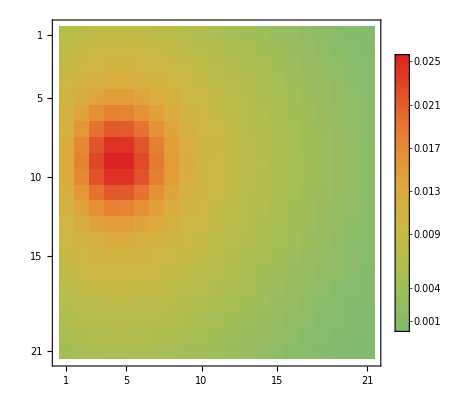

```mathematica
(* compute the transition probabilities from state {n1=8,n2=5} to all other states *)
MatrixPlot[Map[TT[{8,5},#,{{3,3},{4,2}}]&,events,{2}],ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
(* compute the expectation of reward for N rentals given Subscript[λ, rentals] *)
R[n_,λ_List]:=10*∑_(i=0)^n i*N[PDF[PoissonDistribution[λ[[1]]],i]]
```

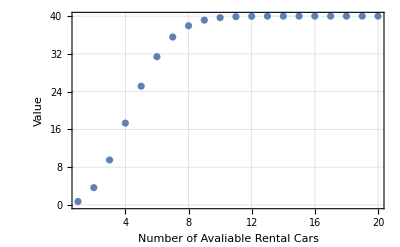

```mathematica
(*visualize the expected returns for N rental cars given Subscript[λ, rentals]*)
ListPlot[
Map[R[#,{4,2}]&,Range[0,19]+1],
GridLines->Automatic,Frame->True, PlotRange -> All,FrameLabel->{
Style["Number of Avaliable Rental Cars",FontSize->12],
Style["Value",FontSize->12]
}
]
```

```mathematica
(* helper function for computing joint reward for given state *)
RR[state_,Λ_]:=Total@MapThread[R,{state,Λ}]
```

```mathematica
(* helper function to give resulting state given current state + action *)
stateGivenAction[s_List,a_]:= {Max[Min[s[[1]]-a,20],0],Max[Min[s[[2]]+a,20],0]};
```

```mathematica
(* function to compute the value of a state s using Belman equation *)
StateValue[s_List,states_List,Λ_List,γ_]:= Total@Flatten@Map[TT[stateGivenAction[s,pi[s]],#,Λ]*(RR[#,Λ]+γ*V[#])&,states,{2}]-2*Abs[pi[s]];
```

```mathematica
(* function to compute the value of a state s GIVEN ACTION using Belman equation *)
StateValue[s_List,action_, states_List,Λ_List,γ_]:= Total@Flatten@Map[TT[stateGivenAction[s,action],#,Λ]*(RR[#,Λ]+γ*V[#])&,states,{2}]-2*Abs[action];
```

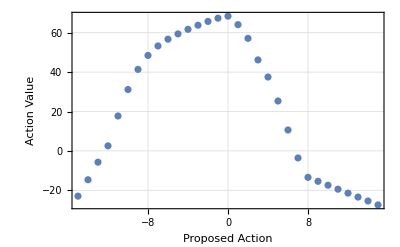

```mathematica
(* compute value of each/all possible actions given state = {15,3} *)
With[{state = {8,17},actions=Range[-15,15]},
ListPlot[Transpose[{actions,ParallelMap[StateValue[state,#,states,{{3,3},{4,2}},0.9]&,actions]}],
Frame->True,GridLines->Automatic,FrameLabel->{Style["Proposed Action",FontSize->12],Style["Action Value",FontSize->12]}]]
```

```mathematica
(* helper function which gives valid actions for a particular state *)
actionsForState[s_List] := Range[-Min[s[[2]],5],Min[s[[1]],5]]
```

```mathematica
(* helper function to compute max value action *)
maxActionValue[s_,Λ_,γ_]:= Module[
{actions,actionValues,maxActionValue,pos},

(* compute all valid actions for this state *)
actions = actionsForState[s];

(* compute value of each valid action *)
actionValues = Map[StateValue[s,#,states,Λ,γ]&,actions];

(*determin maximum action/value*)
maxActionValue=Max@actionValues;pos=Flatten[Position[actionValues,maxActionValue]];

(* return result *)
{maxActionValue,If[pos==={},0,actions[[pos[[1]]]]]}
];
```

```mathematica
(* init delta *)
delta = 99999;

(* keep track of number of iteration *)
iter = 0;

While[ delta > .1,

(* compute updated state values based on current state values V(s), current policy π(s) and discount parameter γ *)
stateValueUpdate = ParallelMap[StateValue[#,states,{{3,3},{4,2}},0.9]&,states,{2}];

(* compute the max difference *)
delta = Max@Flatten@Abs@(Map[V,states,{2}] -stateValueUpdate);

(* update state values, V(s), and policy for number of cars to move, π(s) *)
Table[With[{s = {i-1,j-1}},V[s]=stateValueUpdate[[i,j]];];,{i,1,21},{j,1,21}];

(* update iteration count *)
iter++;
];

(* compute policy update based on current state values *)
policyUpdate = ParallelMap[maxActionValue[#,{{3,3},{4,2}},0.9][[2]]&,states,{2}];

(* update state values, V(s), and policy for number of cars to move, π(s) *)
Table[With[{s = {i-1,j-1}},V[s]=stateValueUpdate[[i,j]]; pi[s]=policyUpdate[[i,j]]];,{i,1,21},{j,1,21}];

(* plot the state value function *)
V =MatrixPlot[stateValueUpdate,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Medium,FrameLabel->{
Style["# Cars at first location",FontSize->12],Style["# Cars at second location",FontSize->12],"",Style["State Value: V(s)",FontSize->12]}];

(* plot the updated policy *)
p = MatrixPlot[policyUpdate,PlotLegends->Automatic,ImageSize->Medium,FrameLabel->{
Style["# Cars at first location",FontSize->12],Style["# Cars at second location",FontSize->12],"",Style["Policy: π(s)",FontSize->12]}];
```